```mathematica
Clear["Global`*"]
```

```mathematica
p[a_,b_] :=((a.b)/(a.a))a;
```

```mathematica
a1 = {1,2,0};
a2 = {0,0,1};
a3 = {-2,1,0};
v1 = a1;
MatrixForm[v1]
```

(1
2
0)

```mathematica
v2 = a2 - p[v1,a2];
MatrixForm[v2]
```

(0
0
1)

```mathematica
v3 = a3-p[v1,a3]-p[v2,a3];
MatrixForm[v3]
```

(-2
1
0)

```mathematica
n[v_] := (1/Sqrt[v.v])v;
q1 = n[v1];
q2 = n[v2];
q3 = n[v3];

FullSimplify[MatrixForm[q1]]
FullSimplify[MatrixForm[q2]]
FullSimplify[MatrixForm[q3]]
```

(1/(√5)
2/(√5)
0)

(0
0
1)

(-2/(√5)
1/(√5)
0)

```mathematica
Solve[a1 == c1 q1,c1]
```

{{c1→3}}

```mathematica
Clear[c1,c2]
Solve[a2 == c1 q1 + c2 q2,{c1,c2}]
```

{{c1→1,c2→√2}}

```mathematica
Clear[c1,c2,c3]
Solve[a3 ==c1 q1 + c2 q2 + c3 q3 ,{c1,c2,c3}]
```

{{c1→2,c2→-√2,c3→√3}}

```mathematica
Clear[c1,c2,c3]
Solve[a4 == c1 q1 + c2 q2 + c3 q3 + c4 q4,{c1,c2,c3,c4}]
```

```mathematica
{{c1->1,c2->1/(√2),c3->-1/(√3),c4->1/(√6)}}
```

```mathematica
MatrixForm[Transpose[{q1,q2, q3, q4}]]
```

(2/3 | -(√2)/3 | 1/(√3) | 0
0 | 1/(√2) | 1/(√3) | -1/(√6)
2/3 | 1/(3 √2) | -1/(√3) | -1/(√6)
1/3 | (√2)/3 | 0 | √(2/3))

```mathematica
A = {{-2,2},{2,-4}}
```

{{-2,2},{2,-4}}

```mathematica
Eigensystem[A]
```

{{-3-√5,-3+√5},{{2+1/2 (-3-√5),1},{2+1/2 (-3+√5),1}}}

```mathematica
7 - 3 √5
```

7-3 √5

```mathematica
Clear[x,y]
```

```mathematica
Solve[{4 x + 6 y == 0,6x +10y==0},{x,y}]
```

{{x→0,y→0}}

```mathematica
Plot3D[- x^2 +2 x y -2 y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

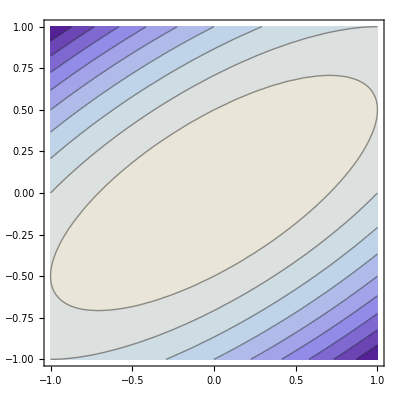

```mathematica
ContourPlot[-x^2 +2x y -2 y^2,{x,-1,1},{y,-1,1}]
```